# Analytical Tests: MCMLpar

## Zachary Levine and Richelle Streater 7 June 2017

```mathematica
style[str_]:= Style[str,Bold,14,FontFamily->"Helvetica"]
```

#### Single scattering probability isotropic finite thickness case

We have a semi-infinite medium with a photon entering at normal incidence.  There is exponential attenuation and isotropic scattering.  What fraction of photons exit the entrance surface on the first reflection?

The photon will exit at an angle θ.  The exit path goes from (0,z) to (x,0).   We have x/z = tan(θ).  x_L below is the Legendre x_L = cosθ, often called μ by others.

The integral is the same whether done in the θ variable or the x_L variable.  Also, we can work in 2D because of symmetry in ϕ.

The three factors in the next equation are: probability distribution of penetration, probability of exit on a diagonal path, and (1/2) because the Legendre x is a uniform distribution over an interval of length 2.

```mathematica
probB[μa_,μs_] := Integrate[ μs Exp[-z*(μs+μa)] Exp[z*(μs+μa) /xL](1/2),{xL,-1,0},{z,0,Infinity}]
```

```mathematica
analyticIvaryμa = Plot[probB[μa,2],{μa,0,10},PlotStyle-> Black];
```

```mathematica
numIvaryμa = {{0,0.1537},{1,0.1024},{3,0.0614},{5,0.0438},{10,0.02558}};
```

```mathematica
numIvaryμaPlot = ListPlot[numIvaryμa,PlotStyle->{Blue,PointSize[0.02]}];
```

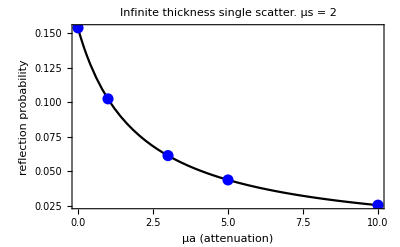

```mathematica
Show[analyticIvaryμa,numIvaryμaPlot,Frame-> True,FrameStyle->Directive[Thick,Black,Bold,12],PlotLabel-> style["Infinite thickness single scatter. μs = 2"],FrameLabel->{style["μa (attenuation)"],style["reflection probability"]}]
```

```mathematica
analyticIvaryμs = Plot[probB[2,μs],{μs,1,10},PlotStyle-> Black];
```

```mathematica
numIvaryμs = {{1,0.05110},{3,0.09195},{5,0.10935},{10,0.12780}};
```

```mathematica
numIvaryμsPlot = ListPlot[numIvaryμs,PlotStyle->{Darker[Cyan],PointSize[0.02]}];
```

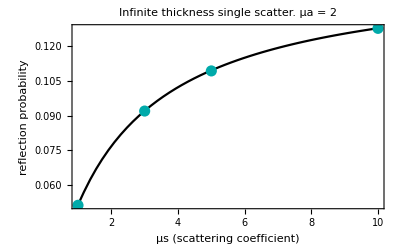

```mathematica
Show[analyticIvaryμs,numIvaryμsPlot,Frame-> True,Axes-> False,PlotLabel-> style["Infinite thickness single scatter. μa = 2"],FrameStyle->Directive[Thick,Black,Bold,12],FrameLabel->{style["μs (scattering coefficient)"],style["reflection probability"]}]
```

#### Extension to finite thickness case

Mathematica would not complete this integral with the chain rule, so it was added in by hand. (horizontally scaled by μs+μa).

```mathematica
probC[t_,μa_, μs_] := μs/(μs+μa)Integrate[ Exp[-z] Exp[-z/xL](1/2),{xL,0,1},{z,0,t},Assumptions->{t>0, μa > 0, μs > 0}]
```

```mathematica
analyticFvaryt=Plot[probC[7*t,2,5],{t,0.01,2},PlotStyle-> Black,PlotRange-> All];
```

```mathematica
numFvaryt = {{0.05,0.06853},{0.1,0.09276},{0.2,0.10644},{2,0.10968}};
```

```mathematica
numFvarytPlot = ListPlot[numFvaryt,PlotStyle->{Darker[Red],PointSize[0.02]}];
```

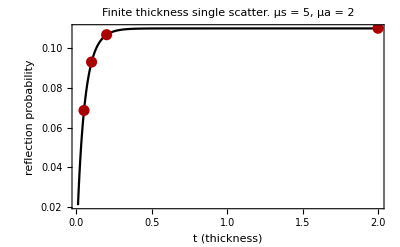

```mathematica
Show[analyticFvaryt,numFvarytPlot,Frame-> True,FrameStyle->Directive[Thick,Black,Bold,12],PlotRange-> All,Axes-> False,PlotLabel-> style["Finite thickness single scatter. μs = 5, μa = 2"],FrameLabel->{style["t (thickness)"], style["reflection probability"]}]
```

#### Extension to Henyey-Greenstein scattering, infinite slab case

```mathematica
pHG[g_,xL_] := (1-g^2)/(2(1+g^2-2 g xL)^(3/2))
```

Mathematica cannot evaluate this function at 0 or 1, so it is easier to test two different regions.  First the positive sign case ...

```mathematica
probE[g_, μa_, μs_] := μs/(μs+μa)Integrate[ Exp[-z] Exp[z /xL]pHG[g,xL],{xL,-1,0},{z,0,Infinity},Assumptions->{0<g<1}]
```

Then the negative sign case ...

```mathematica
probG[g_,μa_, μs_] := μs/(μs+μa)Integrate[ Exp[-z] Exp[z /xL]pHG[g,xL],{xL,-1,0},{z,0,Infinity},Assumptions->{-1<g<0}]
```

These are the same function:

```mathematica
probG[g,μa, μs]==probE[g,μa, μs]
```

True

```mathematica
analyticG = Plot[probE[g, 2, 5], {g,-1,0.999999},FrameLabel->{"g (Henyey-Greenstein phase factor)", "reflection probability"},PlotStyle->Black];
```

```mathematica
numG = {{-1,0.35722},{-0.5,0.23150},{-0.2,0.15450},{0.8,0.00964}};
```

```mathematica
numGPlot = ListPlot[numG,PlotStyle->{Purple,PointSize[0.02]}];
```

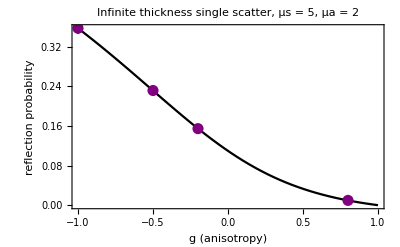

```mathematica
Show[analyticG,numGPlot,Frame-> True,FrameStyle->Directive[Thick,Black,Bold,12],PlotRange-> All,Axes-> False,PlotLabel-> style["Infinite thickness single scatter, μs = 5, μa = 2"],FrameLabel->{style["g (anisotropy)"], style["reflection probability"]}]
```